## BI-CAO Číslicové a analogové obvody 2. cvičení

Cvičící a kontakt: viz tabule nebo rozvrh na https://courses.fit.cvut.cz/BI-CAO/teacher/index.html

Vytvořeno na základě materiálů Miroslava Skrbka a Pavla Kubalíka.
Posledni úpravy: Martin Kohlík před ZS 2019/20

◀     |     ▶

## Seznamy (List)

Seznam je datová struktura, která dovoluje sdružit více položek a definuje nad nimi množinu specifických operací.

Příklad seznamu:

```mathematica
ClearAll["Global`*"]
```

```mathematica
basaPiv={Gambrinus,Plzen,Staropramen}
basaPiv2={Bernard,Svijany,Rohozec}
hromadaPiv={basaPiv,basaPiv,basaPiv2,Starobrno,Radegast}
skladPiv={hromadaPiv,basaPiv2}
```

{Gambrinus,Plzen,Staropramen}

{Bernard,Svijany,Rohozec}

{{Gambrinus,Plzen,Staropramen},{Gambrinus,Plzen,Staropramen},{Bernard,Svijany,Rohozec},Starobrno,Radegast}

{{{Gambrinus,Plzen,Staropramen},{Gambrinus,Plzen,Staropramen},{Bernard,Svijany,Rohozec},Starobrno,Radegast},{Bernard,Svijany,Rohozec}}

Vybrané operace se seznamem:

```mathematica
(* první pivo v base *)
First[basaPiv]
```

Gambrinus

```mathematica
(* přidej nové pivo do basy *)
novaBasaPiv=Append[basaPiv,jesteJednaPlzen]
```

{Gambrinus,Plzen,Staropramen,jesteJednaPlzen}

```mathematica
?List
```

RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}] is a list of elements.

◀     |     ▶

## Přístup k prvkům seznamu (indexace)

K jednotlivým položkám listu lze přistupovat pomocí [[]] (po programátorsku: indexy polí se píšou do dvojitých hranatých závorek)

```mathematica
basaPiv[[2]]
```

Plzen

```mathematica
hromadaPiv[[3]]
```

{Bernard,Svijany,Rohozec}

```mathematica
hromadaPiv[[3,2]]
```

Svijany

```mathematica
skladPiv[[1]]
```

{{Gambrinus,Plzen,Staropramen},{Gambrinus,Plzen,Staropramen},{Bernard,Svijany,Rohozec},Starobrno,Radegast}

```mathematica
skladPiv[[1,2,3]]
```

Staropramen

◀     |     ▶

## Vícerozměrné seznamy

Příkladem vícerozměrného seznamu může být matice (3 | 12 | 5
7 | 9 | 1
22 | 11 | 10)
Seznam odpovídající matici je sestaven po řádcích

```mathematica
matice={{3,12,5},{7,9,1},{22,11,10}}
```

{{3,12,5},{7,9,1},{22,11,10}}

```mathematica
prvekTretiRadekDruhySloupec=matice[[3,2]]
```

11

```mathematica
druhyRadek=matice[[2]]
```

{7,9,1}

```mathematica
prvniSloupec=matice[[All,1]]
```

{3,7,22}

Matice (i vektory) lze také zapsat pomocí palety Basic Math Assistant - sekce Basic Commands - ikona matice (□ | □
□ | □)
Paleta také obsahuje tlačítka pro přidávaní řádků (Ctrl + ⌤) a sloupců (Ctrl + ,).

```mathematica
matice2=({{3, 12, 5}, {7, 9, 1}, {22, 11, 10}})
matice2[[3,2]]
```

{{3,12,5},{7,9,1},{22,11,10}}

11

◀     |     ▶

## Funkce operující nad listy

```mathematica
?Flatten
```

RowBox[{"Flatten", "[", StyleBox["list", "TI"], "]"}] flattens out nested lists. 
RowBox[{"Flatten", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] flattens to level StyleBox["n", "TI"]. 
RowBox[{"Flatten", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["h", "TI"]}], "]"}] flattens subexpressions with head StyleBox["h", "TI"]. 
RowBox[{"Flatten", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["s", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["s", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["s", "TI"], StyleBox["21", "TR"]], ",", SubscriptBox[StyleBox["s", "TI"], StyleBox["22", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] flattens StyleBox["list", "TI"] by combining all levels SubscriptBox[StyleBox["s", "TI"], StyleBox["ij", "TI"]] to make each level StyleBox["i", "TI"] in the result.

```mathematica
velkaHromadaPiv=Flatten[skladPiv]
```

{Gambrinus,Plzen,Staropramen,Gambrinus,Plzen,Staropramen,Bernard,Svijany,Rohozec,Starobrno,Radegast,Bernard,Svijany,Rohozec}

```mathematica
?Sort
```

RowBox[{"Sort", "[", StyleBox["list", "TI"], "]"}] sorts the elements of StyleBox["list", "TI"] into canonical order. 
RowBox[{"Sort", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["p", "TI"]}], "]"}] sorts using the ordering function StyleBox["p", "TI"].

```mathematica
srovnanaHromadaPiv=Sort[velkaHromadaPiv]
```

{Bernard,Bernard,Gambrinus,Gambrinus,Plzen,Plzen,Radegast,Rohozec,Rohozec,Starobrno,Staropramen,Staropramen,Svijany,Svijany}

```mathematica
?Union
```

RowBox[{"Union", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] gives a sorted list of all the distinct elements that appear in any of the SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Union", "[", StyleBox["list", "TI"], "]"}] gives a sorted version of a list, in which all duplicated elements have been dropped.

```mathematica
prebranaHromadaPiv=Union[velkaHromadaPiv]
```

{Bernard,Gambrinus,Plzen,Radegast,Rohozec,Starobrno,Staropramen,Svijany}

Další funkce lze najít v nápovědě (List Manipulation).

◀     |     ▶

## Funkce generující listy

```mathematica
?Range
```

RowBox[{"Range", "[", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], "]"}] generates the list RowBox[{"{", RowBox[{"1", ",", "2", ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]. 
RowBox[{"Range", "[", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "]"}] generates the list RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]. 
RowBox[{"Range", "[", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], ",", StyleBox["di", "TI"]}], "]"}] uses step StyleBox["di", "TI"].

```mathematica
Range[3,30]
Range[3,30,6]
```

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

{3,9,15,21,27}

```mathematica
?Table
```

RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] generates a list of StyleBox["n", "TI"] copies of StyleBox["expr", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a list of the values of StyleBox["expr", "TI"] when StyleBox["i", "TI"] runs from 1 to SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] starts with RowBox[{StyleBox["i", "TI"], "=", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]]}]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], ",", StyleBox["di", "TI"]}], "}"}]}], "]"}] uses steps StyleBox["di", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] uses the successive values SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ….
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["j", "TI"], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] gives a nested list. The list associated with StyleBox["i", "TI"] is outermost.

```mathematica
Table[x^2,{x,0,10}]
```

{0,1,4,9,16,25,36,49,64,81,100}

Další funkce lze najít v nápovědě (Constructing Lists).

◀     |     ▶

## Řešení soustavy lineárních rovnic

S řešením soustavy lineárních rovnic o dvou neznámých jste se setkali na střední škole.

Řešte následující soustavu rovnic
3x+2y=0
6x-4y=1

Použijeme funkci Solve

```mathematica
ClearAll["Global`*"]
Solve[{3x+2y==0,6x-4y==1},{x,y}]
```

{{x→1/12,y→-1/8}}

Matematické rovná se (=) se v programu Mathematica zapisuje jako == (dvě rovná se za sebou). Výsledkem výrazu je True (pravda) nebo False (nepravda). Například 5==6 dává False, ale 5==(6-1) dává True. Operátor == má prakticky stejný význam jako v jazycích C nebo Java.

Druhým parametrem funkce Solve je seznam neznámých proměnných.

◀     |     ▶

## Řešení soustavy diferenciálních rovnic

Diferenciální rovnice a jejich soustavy lze řešit v Mathematice buď analyticky pomocí funkce DSolve (výsledkem je funkce) nebo numericky pomocí NDSolve (výsledkem je popis grafu funkce pomocí interpolační funkce).
Hlavním rozdílem oproti klasickým lineárním rovnicím je nahrazení neznámých (x, y) za funkce (x[t], y[t]) a jejich derivace.

Řešte následující soustavu rovnic
3x[t]+2y[t]=x'[t]
6x[t]-4y[t]=1

Použijeme funkci DSolve

```mathematica
ClearAll["Global`*"]
DSolve[{3x[t]+2y[t]==x'[t],6x[t]-4y[t]==1},{x[t],y[t]},t]
```

{{x[t]→1/25 (25/12+ⅇ^(6 t) C[1]),y[t]→-1/4+3/50 (25/12+ⅇ^(6 t) C[1])}}

V rovnicích je opět nutno použít == (dvě rovná se za sebou).

Druhým parametrem funkce DSolve je seznam neznámých funkcí, třetí parametr je tzv. nezávisle proměnná, tj. ta proměnná, která se vyskytuje uvnitř závorek všech neznámých funkcí.

Ve výsledku řešení diferenciálních rovnic se vyskytuje konstanta C[1], kterou lze odstranit zadáním tzv. počáteční podmínky do soustavy. Soustava diferenciálních rovnic sice vypočítá tvar výsledné funkce, ale její přesné umístění je určeno právě počáteční podmínkou.

```mathematica
ClearAll["Global`*"]
resDS=DSolve[{3x[t]+2y[t]==x'[t],6x[t]-4y[t]==1,x[0]==0},{x[t],y[t]},t]
```

{{x[t]→1/12 (1-ⅇ^(6 t)),y[t]→1/8 (-1-ⅇ^(6 t))}}

◀     |     ▶

## Numerické řešení soustavy diferenciálních rovnic

Parametry numerického řešení pomocí NDSolve jsou velmi podobné jako u analytického řešení pomocí DSolve, pouze u třetího parametru je třeba zadat rozsah odkud kam bude výpočet probíhat.
Výsledek je pak možno použít jen v tomto rozsahu!

```mathematica
resNDS=NDSolve[{3x[t]+2y[t]==x'[t],6x[t]-4y[t]==1,x[0]==0},{x[t],y[t]},{t,0,1}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

Ve výsledku numerického řešení jsou vidět náhledy tvarů grafů všech neznámých funkcí.

Porovnání analytického a numerického řešení:

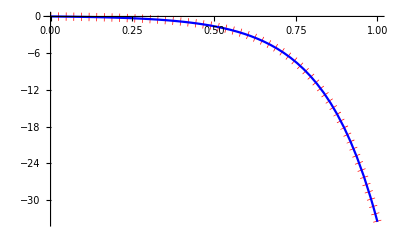

```mathematica
Plot[{x[t]/.resDS[[1]],x[t]/.resNDS[[1]]},{t,0,1},PlotStyle->{{Red,Dotted,Thickness[0.015]},{Blue}}]
```

Porovnání analytického a numerického řešení mimo rozsah NDSolve:

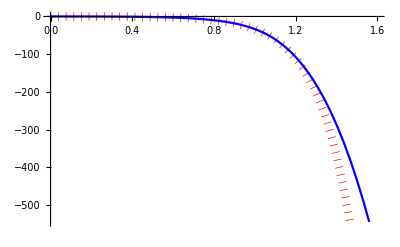

```mathematica
Plot[{x[t]/.resDS[[1]],x[t]/.resNDS[[1]]},{t,0,1.6},PlotStyle->{{Red,Dotted,Thickness[0.015]},{Blue}}]
```

◀     |     ▶

## Proměnné - rozšířené možnosti

Hodnotou proměnné může být nejenom číslo, ale prakticky jakýkoliv výraz či řetězec. Například:

```mathematica
x=5
budova=NTK
```

5

NTK

Proměnné lze proto využít například pro pojmenování složitých výrazů, například rovnic. Soustavu lineárních rovnic

2a + 3b + 4.2c == 5
3a + 15.2b + 8.7c == 80.1
4a + 8.9b + 17.2c == 11

lze proto řešit buď takto:

```mathematica
Solve[{2a+3b+4.2c==5,3a+15.2b+8.7c ==80.1,4a+8.9b+17.2c ==11}]
```

{{a→-3.63596,b→7.29908,c→-2.29174}}

nebo takto:

```mathematica
rce1=2a+3b+4.2c==5;
rce2=3a+15.2b+8.7c==80.1;
rce3=4a+8.9b+17.2c==11;
Solve[{rce1,rce2, rce3}]
```

{{a→-3.63596,b→7.29908,c→-2.29174}}

proměnná | hodnota
rce1 | 2a+3b+4.2c==5
rce2 | 3a+15.2b+8.7c==80.1
rce3 | 4a+8.9b+17.2c==11

◀     |     ▶

## Pravidla

```mathematica
ClearAll[x]
```

```mathematica
def={x->2,y->1,z->4}
moje={x-> 5}
{x,y,z}/.moje
({x,y,z}/.moje)/.def
```

{x→2,y→1,z→4}

{x→5}

{5,y,z}

{5,1,4}

"→"  se napíše tak, že zadáte - následované > a pak pokračujete v psaní. Stejný znak se používá i nepovinných parametrů (např.: Plot[Sin[x],{x,0,1},PlotStyle→Red])
Pozor při kopírování z pdf souborů, textových polí a ze stránek Courses! Často zkopírují netisknutelné a neviditelné znaky - problémy jsou zejména právě se znakem →, ale i s uvozovkami, indexy apod.

```mathematica
spatne=x->2;(*RightArrow*)
dobre=x->2;(*Rule*)
x/.spatne
x/.dobre
```

ReplaceAll::reps: {x→2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.x→2

2

```mathematica
FullForm[spatne]
FullForm[dobre]
```

RightArrow[x,2]

Rule[x,2]

◀     |     ▶

## Použití pravidel

S pravidly se setkáme nejčastěji jako s výsledkem funkce Solve (DSolve i NDSolve):

```mathematica
rce1=2a+3b+4.2c==5;
rce2=3a+15.2b+8.7c==80.1;
rce3=4a+8.9b+17.2c==11;
reseni=Solve[{rce1,rce2, rce3}]
a/.reseni
a+2*b/.reseni[[1]]
```

{{a→-3.63596,b→7.29908,c→-2.29174}}

{-3.63596}

10.9622

Je ale možné je použít i jako jednorázové dosazení v případě, že nechceme nedopatřením přepsat původní výraz

```mathematica
ClearAll["Global`*"]
```

Při prvním odpálení následující buňky je výsledek v pořádku, ale při druhém se vykreslí už jen rovná čára - do původního výrazu se při druhém odpálení uložila již dosazená konstanta x.

Cos[x]+Sin[x]

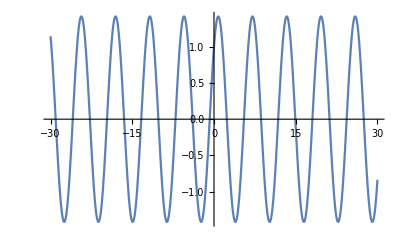

-1

```mathematica
mujVyraz=Sin[x]+Cos[x]
Plot[mujVyraz,{x,-30,30}]
x=π;
mujVyraz
```

```mathematica
ClearAll["Global`*"]
```

Následující buňku lze odpalovat opakovaně beze změny výsledku - aplikací pravidla se do x ani do výrazu nic neuložilo

```mathematica
mujVyraz=Sin[x]+Cos[x]
Plot[mujVyraz,{x,-30,30}]
mujVyraz/.x->π
```

Cos[x]+Sin[x]

-Graphics-

-1

◀     |     ▶

## Práce s maticemi (vícerozměrnými seznamy)

Zobrazení matice v matematickém tvaru pomocí MatrixForm:

```mathematica
ClearAll["Global`*"];
matice={{3,12,5},{7,9,1},{22,11,10}}
MatrixForm[matice]
```

{{3,12,5},{7,9,1},{22,11,10}}

(3 | 12 | 5
7 | 9 | 1
22 | 11 | 10)

Pozor: Neukládejte MatrixForm[matice] do proměnné - Mathematica by pak už takovou matici neuměla dále zpracovat.
MatrixForm (a ostatní příkazy typu *Form - viz nápověda) slouží pouze pro zobrazení výsledku v čitelnější formě.

Tip: Pro příkazy typu *Form je výhodná postfixová notace zápisu.

```mathematica
matice//MatrixForm
```

(3 | 12 | 5
7 | 9 | 1
22 | 11 | 10)

Maticové operátory a výpočty (viz nápověda Matrix Operations):

```mathematica
matice={{3,12,5},{7,9,1},{22,11,10}};
matice2=({{1, 2, 5}, {7, 8, 1}, {1, 4, 3}});
matice+matice2//MatrixForm (*součet*)
Transpose[matice]//MatrixForm (*tranzpozice*)
{a,b,c}.{x,y,z} (*skalární součin*)
{{a,b},{c,d}}*{x,y}//MatrixForm (*maticový součin*)
```

(4 | 14 | 10
14 | 17 | 2
23 | 15 | 13)

(3 | 7 | 22
12 | 9 | 11
5 | 1 | 10)

a x+b y+c z

(a x | b x
c y | d y)

◀     |     ▶

## Derivace a integrály

Múžeme je napsat pomocí funkcí, nebo pomocí palety BasicMath Assistant v sekci Basic Commands:

```mathematica
D[x^n,x]
D[x^n, x]
```

n x^(-1+n)

n x^(-1+n)

Derivaci uživatelsky definované funkce můžeme napsat i pomocí apostrofu:

```mathematica
mojeFce[x_]:=x^n
mojeFce'[x]
```

n x^(-1+n)

```mathematica
Integrate[n x^(-1+n),x]
∫n x^(-1+n)ⅆx
```

x^n

x^n

Určitý integrál:

```mathematica
Integrate[ⅇ^-x,{x,1,Infinity}]
∫_1^∞ ⅇ^-x ⅆx
```

1/ⅇ

1/ⅇ

◀     |     ▶

## Boolova algebra

Výrazy můžeme psát v programátorském i matematickém tvaru:

```mathematica
a||b&&!c
boolVyraz=a∨b∧¬c
```

a||(b&&!c)

a||(b&&!c)

```mathematica
boolVyraz//TraditionalForm
```

a∨(b∧¬c)

Generování tabulky a mapy z funkce:

```mathematica
BooleanTable[boolVyraz,{a,b,c}] (*začíná od samých 1 (True)*)
```

{True,True,True,True,False,True,False,False}

```mathematica
BooleanTable[boolVyraz,{a},{b},{c}]//TableForm
```

True
True | True
True
False
True | False
False

Minimalizace výrazu a test tautologie:

```mathematica
BooleanMinimize[a∧b∨¬a∧b]
```

b

```mathematica
TautologyQ[(a||b)||(!a&&!b),{a,b}]
```

True

Další funkce lze najít v nápovědě (Boolean Computation).

◀     |     ▶

## Wolfram Alpha

K dispozici na adrese http://www.wolframalpha.com/ i bez nainstalované Mathematicy.
Výrazy můžeme zadávat v syntaxi Mathematicy i v běžné angličtině.
Z Mathematicy lze zadat dotaz pro Wolfram Alpha pomocí znaků ==, které zadáme na začátku nové buňky.

ursa major

iss today

Answer to the Ultimate Question of Life, the Universe, and Everything

Doctor John Zoidberg-like curve

◀     |     ▶